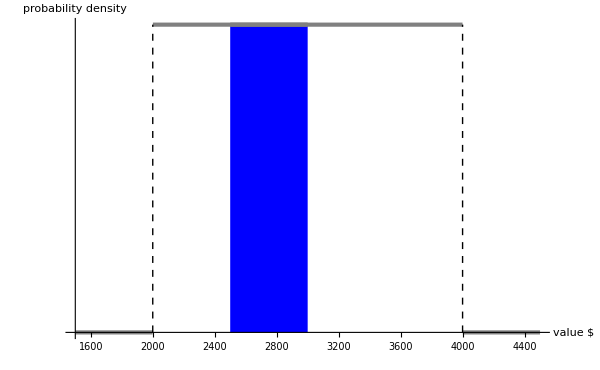

```mathematica
dist=PDF[UniformDistribution[{2000,4000}],#]&;
p1=Plot[dist@x,{x,2500,3000},Filling->Axis,FillingStyle->Blue,BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{"value $ ","probability density "},PlotRange->{{1500,4500},Full},Ticks->{True,False}];
p2=Plot[dist@x,{x,1500,4500},Filling->None,PlotRange->{{1500,4500},Full},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{"value $ ","p(v)"}];
Show[p1,p2,Epilog->{{Dashed,Line[{{2000,0},{2000,1/2000}}]},{Dashed,Line[{{4000,0},{4000,1/2000}}]}},ImageSize->600]
```